```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
QuantumState["000"]//TraditionalForm
```

000

```mathematica
QuantumOperator["X"]//TraditionalForm
QuantumOperator["Z"]//TraditionalForm
QuantumOperator["CNOT"]//TraditionalForm
QuantumOperator["H"]//TraditionalForm
```

01+10

00-11

0000+0101+1011+1110

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

-ⅈ01+ⅈ10

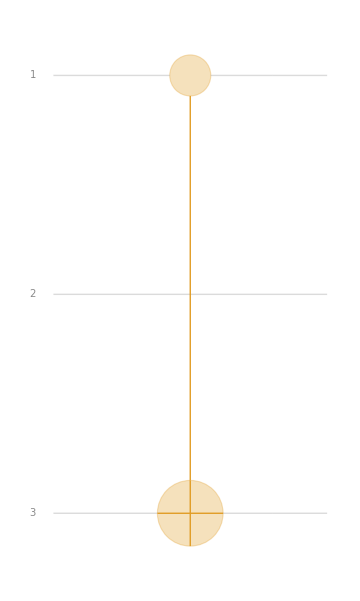

```mathematica
QuantumOperator[{"CNOT"->{1,3}}]["CircuitDiagram"]
```

```mathematica
QuantumOperator["CNOT"]
```

QuantumCircuitOperator[…]

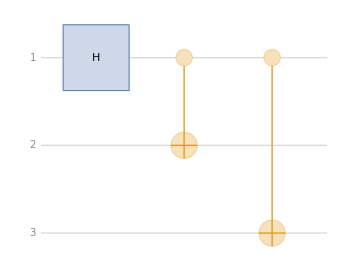

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

0000+0101+1011+1110

0000+0101+1011+1110

1/(√2)000+1/(√2)111

```mathematica
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CNOT"->{1,2}],
	QuantumOperator["CNOT"->{1,3}]
]]
qc["Diagram"]
QuantumOperator["H",{1}]//TraditionalForm
QuantumOperator["CNOT"->{1,2}]//TraditionalForm
QuantumOperator["CNOT"->{1,3}]//TraditionalForm
qc[QuantumState["000"]]//TraditionalForm
```

```mathematica
qc["Diagram"]
```

```mathematica
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}]
]]
qc[QuantumState["000"]]//TraditionalForm
```

QuantumCircuitOperator[…]

1/(√2)000+1/(√2)100